## NLL Angularities with Shape Function

### Baseline Values

```mathematica
αsCR baseline=(*0.117998;*)0.1185;
NF baseline = 5;
Ω0 baseline = 0.500;  (*in GeV this number needs to be checked *)
Ω0 tiny = 0.00001; (* used for quasi-parton cross check *)
```

### Physical Constants

```mathematica
mZ=91.19;
β0=11/(4π)-5/(6π);
β1=153/(24 π^2)-75/(24 π^2)-20/(24 π^2);
K=(67/6-π^2/2)-25/9;
CF = 4/3;
CA = 3;
Bq =-3/4;
Bg[NF_]:=-(33-2NF)/36;
aNGL = 0.85*CA;
bNGL = 0.86*CA;
cNGL = 1.33;
```

### Angularites: Perturbative Cumulative Distribution

```mathematica
AngularitiesMasterCumulative[τ1_, Cfactor_, Bfactor_,αsCR_,  R_, Q_, use2loop_, useNGL_, β_]:= Block[{L,t, NGL, αs,λ, r,T,Talt,dr,ANS, kt},

kt = Q* R /2.0; (* factor of two because jet energy is half of collision energy in e+e-*)
L=Log[1/τ1];
αs=(1/αsCR+23/(6π)Log[kt/mZ]+116/(92π)Log[1+23/(6π)αsCR Log[kt/mZ]])^-1;
λ=αs*β0*L;
r=L/(2π β0 λ(β-1))((1-2λ)Log[1-2λ]-(β-2λ)Log[1-(2λ)/β])+use2loop*1/(β-1)(K/(4 π^2 β0^2)(β Log[1-(2λ)/β]-Log[1-2λ])+β1/(2π β0^3)(Log[1-2λ]^2/2-β/2 Log[1-(2λ)/β]^2+Log[1-2λ]-β Log[1-(2λ)/β]));
T=-1/(π β0)Log[1-2λ];
t = T/4;
Talt=-1/(π β0)Log[1-(2λ)/β];
dr=1/(β-1)(T-Talt);

NGL = Exp[-useNGL* Cfactor *CA π^2/3((1 + (aNGL*t)^2)/(1 + (bNGL*t)^cNGL) )t^2];

ANS =NGL* ⅇ^(-EulerGamma Cfactor dr)/Gamma[1+Cfactor dr] ⅇ^(-Cfactor(r+Bfactor  Talt));
If[1-2λ>0 && 1-(2λ)/β>0 && αs>0,Evaluate[ANS],0.0]
]
```

### Defining Benchmarks

```mathematica
(* Baseline*)
AngularitiesCumulative[τ1_,"baseline","quark", R_, Q_, β_]:= AngularitiesMasterCumulative[τ1, CF, Bq, αsCR baseline, R, Q, 1,1, β]
AngularitiesCumulative[τ1_,"baseline","gluon", R_, Q_, β_]:= AngularitiesMasterCumulative[τ1, CA, Bg[NF baseline], αsCR baseline, R, Q, 1,1,β]

(* No g -> qq , only gluon has to change *)
AngularitiesCumulative[τ1_,"nogqq","quark", R_, Q_, β_]:=AngularitiesMasterCumulative[τ1, CF, Bq, αsCR baseline, R, Q, 1,1,β]
AngularitiesCumulative[τ1_,"nogqq","gluon", R_, Q_ ,β_]:= AngularitiesMasterCumulative[τ1, CA, Bg[0], αsCR baseline, R, Q, 1,1,β]

(* No 2loop effects *)
AngularitiesCumulative[τ1_,"no2loop","quark", R_, Q_, β_]:= AngularitiesMasterCumulative[τ1, CF, Bq, αsCR baseline, R, Q, 0, 1,β]
AngularitiesCumulative[τ1_,"no2loop","gluon", R_, Q_, β_]:= AngularitiesMasterCumulative[τ1, CA, Bg[NF baseline], αsCR baseline, R, Q, 0,1,β]

(* No NGL effects *)
AngularitiesCumulative[τ1_,"noNGL","quark", R_, Q_, β_]:= AngularitiesMasterCumulative[τ1, CF, Bq, αsCR baseline, R, Q, 1, 0,β]
AngularitiesCumulative[τ1_,"noNGL","gluon", R_, Q_, β_]:= AngularitiesMasterCumulative[τ1, CA, Bg[NF baseline], αsCR baseline, R, Q, 1,0,β]

(* αs sweep *)
AngularitiesCumulative[τ1_,"alphasx08","quark", R_, Q_, β_]:= AngularitiesMasterCumulative[τ1, CF, Bq, 0.8*αsCR baseline, R, Q,1,1, β]
AngularitiesCumulative[τ1_,"alphasx09","quark", R_, Q_, β_]:= AngularitiesMasterCumulative[τ1, CF, Bq, 0.9*αsCR baseline, R, Q,1, 1,β]
AngularitiesCumulative[τ1_,"alphasx10","quark", R_, Q_, β_]:= AngularitiesMasterCumulative[τ1, CF, Bq, 1*αsCR baseline, R, Q,1, 1,β]
AngularitiesCumulative[τ1_,"alphasx11","quark", R_, Q_, β_]:= AngularitiesMasterCumulative[τ1, CF, Bq, 1.1*αsCR baseline, R, Q,1, 1,β]
AngularitiesCumulative[τ1_,"alphasx12","quark", R_, Q_, β_]:= AngularitiesMasterCumulative[τ1, CF, Bq, 1.2*αsCR baseline,R, Q,1,1, β]

AngularitiesCumulative[τ1_,"alphasx08","gluon", R_, Q_, β_]:= AngularitiesMasterCumulative[τ1, CA, Bg[NF baseline], 0.8*αsCR baseline, R, Q, 1,1,β]
AngularitiesCumulative[τ1_,"alphasx09","gluon", R_, Q_, β_]:= AngularitiesMasterCumulative[τ1, CA, Bg[NF baseline], 0.9*αsCR baseline, R, Q,1, 1,β]
AngularitiesCumulative[τ1_,"alphasx10","gluon", R_, Q_, β_]:= AngularitiesMasterCumulative[τ1, CA, Bg[NF baseline], 1*αsCR baseline, R, Q,1, 1,β]
AngularitiesCumulative[τ1_,"alphasx11","gluon", R_, Q_, β_]:= AngularitiesMasterCumulative[τ1, CA, Bg[NF baseline], 1.1*αsCR baseline, R, Q,1, 1,β]
AngularitiesCumulative[τ1_,"alphasx12","gluon", R_, Q_, β_]:= AngularitiesMasterCumulative[τ1, CA, Bg[NF baseline], 1.2*αsCR baseline,R, Q,1, 1,β]
```

### Angularities: Perturbative Differential Distribution and Lists/Interpolations

```mathematica
(* defining generic parton-level*)
Clear[AngularitiesDifferentialList, AngularitiesDifferentialInterpolation]

(* Have to start with zero for this to work*)
τ1max = 1;
τ1nbins = 1000;
τ1diff = τ1max/τ1nbins;
τ1order = 1;

AngularitiesDifferentialList[ "parton",para_, sample_, R_,Q_,β_]:=  AngularitiesDifferentialList[ "parton", para, sample, R,Q, β] =Block[{cumlist, cumlistL, cumlistR, centers, derivs},
cumlist = Join[{{0,0}},Table[{τ1,Max[Re[AngularitiesCumulative[τ1 , para, sample, R,Q,β]],0.0]}, {τ1,τ1diff,τ1max-τ1diff,τ1diff}],{ {τ1max,1}}]; 
cumlistL = Rest[cumlist];
cumlistR = Most[cumlist];

centers = (cumlistL[[All,1]] + cumlistR[[All,1]])/2;
derivs = (cumlistL[[All,2]] - cumlistR[[All,2]])/τ1diff;
derivs =  Max[#,0]&/@ derivs;
derivs = derivs/Total[derivs]/τ1diff;
 Transpose[{centers,derivs}] 
]

AngularitiesDifferentialInterpolation[type_, para_, sample_, R_,Q_, β_]:= AngularitiesDifferentialInterpolation[type, para, sample, R,Q, β] = Interpolation[AngularitiesDifferentialList[type, para, sample, R,Q, β], InterpolationOrder->τ1order]
```

### Non-perturbative Corrections

```mathematica
(*GenericShapeFunction[δ_, δ0_]:= (4δ)/δ0^2 ⅇ^(-(2δ)/δ0)*)
GenericShapeCumulative[δ_,δ0_]:= 1-ⅇ^(-(π δ^2)/(4 δ0^2)) (*(δ0-ⅇ^(-(2 δ)/δ0) (2 δ+δ0))/δ0; *) (*  1-ⅇ^(-(π δ^2)/(4 δ0^2))*) 

(* Dividing by 2 since Q is collision energy, but power correction is related to jet energy *)
AngularitiesNonPerturbativeShift[Ω0_,R_, Q_, β_]:=Ω0/(R* Q/2.0) (1 - ((Ω0 * 3)/(R*Q/2.0))^(β-1))/(β - 1);

color of["quark"]:= CF;
color of["gluon"]:= CA;

ShapeCumulative[δ_,"hadron",para_, sample_,  R_,Q_,β_]:= GenericShapeCumulative[δ, AngularitiesNonPerturbativeShift[color of[sample]* Ω0 baseline,R,Q, β]]
ShapeCumulative[δ_,"quasi-parton",para_, sample_,R_,Q_ ,β_]:= GenericShapeCumulative[δ,AngularitiesNonPerturbativeShift[Ω0 tiny,R,Q, β]]

Clear[ShapeDifferentialList]

ShapeDifferentialList[type_,para_, sample_,R_,Q_, β_]:=  ShapeDifferentialList[type, para, sample, R,Q,β] =Block[{cumlist, cumlistL, cumlistR, centers, derivs},
cumlist = Join[{{0,0}},Table[{τ1,Max[Re[ShapeCumulative[τ1 ,type, para, sample,R,Q, β]],0.0]}, {τ1,τ1diff,τ1max-τ1diff,τ1diff}],{{τ1max ,1}}]; 
cumlistL = Rest[cumlist];
cumlistR = Most[cumlist];

centers = (cumlistL[[All,1]] + cumlistR[[All,1]])/2;
derivs = (cumlistL[[All,2]] - cumlistR[[All,2]])/τ1diff;
(* next two steps probably aren't needed, but putting in anyways *)
derivs =  Max[#,0.0]&/@ derivs;
derivs = derivs/Total[derivs]/τ1diff;
 Transpose[{centers,derivs}] 
]


(* This technique only works if parton and shape have the same length, parton and shape have zero entries at 0, and equally spaced yada yada *)
AngularitiesDifferentialList[ type_,para_, sample_, R_,Q_,β_]:=  AngularitiesDifferentialList[ type, para, sample, R,Q, β]  = Block[{parton, shape,coords, values, total, shifted},
parton = AngularitiesDifferentialList[ "parton", para, sample,R,Q,  β];
shape = ShapeDifferentialList[type, para, sample,R,Q,  β];

(* This technique only works if parton and shape have the same length, parton and shape have zero entries at 0, and equally spaced yada yada *)
coords = parton[[All,1]];
values =  parton[[All,2]];

total = Table[0, {k,1, Length[parton]}];

For[i=1, i < Length[shape], i++,
total += shape[[i,2]]*values*τ1diff;
values = Join[{0},Most[values]];
];

Transpose[{coords,total}]
]
```

## Outputting Distributions

```mathematica
SetDirectory[NotebookDirectory[]]

R baseline  = 0.6;
R values = {0.2,0.4,0.6,0.8,1.0}
R name[0.2]= "R02";
R name[0.4]= "R04";
R name[0.6]= "R06";
R name[0.8]= "R08";
R name[1.0]= "R10";

Q baseline = 200.0 ;
Q values = {50,100,200,400,800}
Q name[50]= "50";
Q name[100]= "100";
Q name[200]= "200";
Q name[400]= "400";
Q name[800]= "800";

β baseline = 0.5 ;
βone = 1.0001;
β values = {0.5,βone,2.0};
β name[0.5] = "beta05";
β name[βone] = "beta10";
β name[2.0] = "beta20";

MakeMinMax[{xmin_,value_}]:= {N[xmin- τ1diff/2],N[xmin+ τ1diff/2],N[Round[value*100000]/100000]}

OutputFilesForSetting[para_, R_, Q_, β_]:= Module[{one,two,three,four},
one =  MakeMinMax/@ AngularitiesDifferentialList["parton",para,"quark", R,Q,β];
Export["parton/uu-"<>Q name[Q]<>"-"<>If[para == "baseline", "", para<>"-"]<> β name[β] <> "-" <>R name[R]<>".txt",one, "Table"];
two = MakeMinMax/@ AngularitiesDifferentialList["parton",para,"gluon", R,Q,β];
Export["parton/gg-"<>Q name[Q]<>"-"<>If[para == "baseline", "", para<>"-"]<> β name[β] <> "-" <>R name[R]<>".txt",two, "Table"];
three = MakeMinMax/@ AngularitiesDifferentialList["hadron",para,"quark", R,Q,β];
Export["hadron/uu-"<>Q name[Q]<>"-"<>If[para == "baseline", "", para<>"-"]<> β name[β] <> "-" <>R name[R]<>".txt",three, "Table"];
four = MakeMinMax/@ AngularitiesDifferentialList["hadron",para,"gluon", R,Q,β];
Export["hadron/gg-"<>Q name[Q]<>"-"<>If[para == "baseline", "", para<>"-"]<> β name[β] <> "-" <>R name[R]<>".txt",four, "Table"];
]

OutputFilesForSetting[para_]:= Module[{},
Outer[OutputFilesForSetting[para, #1,#2,#3]&, R values, Q values, β values]
]
```

/Users/jthaler/outside/lh2015-qg/AnalyticResum

{0.2,0.4,0.6,0.8,1.}

{50,100,200,400,800}

```mathematica
OutputFilesForSetting["baseline"]
```

{{{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null}},{{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null}},{{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null}},{{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null}},{{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null}}}

```mathematica
OutputFilesForSetting["nogqq"]
```

{{{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null}},{{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null}},{{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null}},{{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null}},{{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null}}}

```mathematica
OutputFilesForSetting["no2loop"]
OutputFilesForSetting["noNGL"]
OutputFilesForSetting["alphasx08"]
OutputFilesForSetting["alphasx09"]
OutputFilesForSetting["alphasx10"]
OutputFilesForSetting["alphasx11"]
OutputFilesForSetting["alphasx12"]
```

{{{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null}},{{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null}},{{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null}},{{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null}},{{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null}}}

{{{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null}},{{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null}},{{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null}},{{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null}},{{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null}}}

{{{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null}},{{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null}},{{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null}},{{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null}},{{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null},{Null,Null,Null}}}

«4 more identical outputs»

## Binning and Classifier Separation

```mathematica
QGClassifierSeparation[type_, para_, R_,Q_,β_]:= Block[{quarklist, gluonlist,answer, integrand},
quarklist = AngularitiesDifferentialList[type, para, "quark",R,Q, β][[All,2]];
gluonlist = AngularitiesDifferentialList[type, para, "gluon",R,Q, β][[All,2]];
integrand = (quarklist - gluonlist + ϵ)^2 / (2(quarklist+gluonlist + ϵ)) /. ϵ -> 0;
answer = Total[integrand]*τ1diff
]
```

## Checking Partonic Results

### Basic Partonic Distribution

QGClassifierSeparation[parton,baseline,0.6,200.,0.5]

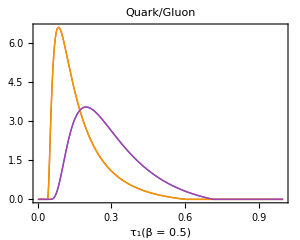
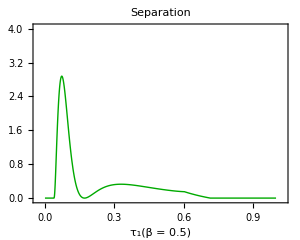

```mathematica
QGClassifierSeparation["parton", "baseline",R baseline, Q baseline, β baseline]
{
Plot[{
AngularitiesDifferentialInterpolation["parton", "baseline","quark",R baseline, Q baseline,β baseline][τ1],
AngularitiesDifferentialInterpolation["parton", "baseline","gluon",R baseline, Q baseline,β baseline][τ1],
AngularitiesDifferentialInterpolation["quasi-parton", "baseline","quark",R baseline, Q baseline,β baseline][τ1],
AngularitiesDifferentialInterpolation["quasi-parton", "baseline","gluon",R baseline, Q baseline,β baseline][τ1]
},{τ1,τ1diff/2.0,τ1max-τ1diff/2.0},PlotLabel-> "Quark/Gluon",
PlotRange->All,PlotStyle->Thick, Frame-> True, FrameStyle -> Thickness[Medium], FrameLabel->{"τ_1(β = 0.5)", ""}, ImageSize -> 300, PlotTheme->{ "Scientific","Frame"}, AspectRatio-> 0.8]
,
Plot[{
(AngularitiesDifferentialInterpolation["parton", "baseline","quark",R baseline, Q baseline,β baseline][τ1] - AngularitiesDifferentialInterpolation["parton", "baseline","gluon",R baseline, Q baseline,β baseline][τ1])^2/(2(AngularitiesDifferentialInterpolation["parton", "baseline","quark",R baseline, Q baseline,β baseline][τ1] + AngularitiesDifferentialInterpolation["parton", "baseline","gluon",R baseline, Q baseline,β baseline][τ1] + 0.000000000001))},{τ1,τ1diff/2.0,τ1max-τ1diff/2.0},PlotLabel-> "Separation",
PlotStyle->Directive[Thick,Darker[Green]], Frame-> True, FrameStyle -> Thickness[Medium], FrameLabel->{"τ_1(β = 0.5)", ""}, ImageSize -> 300, PlotTheme->{ "Scientific","Frame"}, AspectRatio-> 0.8, PlotRange-> {{-0.03,1.03}, {-0.03,4.03}}]
}
```

```mathematica
{QGClassifierSeparation["parton", "baseline",R baseline, Q baseline, 0.5],QGClassifierSeparation["parton", "baseline",R baseline, Q baseline, βone],QGClassifierSeparation["parton", "baseline",R baseline, Q baseline, 2.0]}
{QGClassifierSeparation["parton", "nogqq",R baseline, Q baseline, 0.5],QGClassifierSeparation["parton", "nogqq",R baseline, Q baseline, βone],QGClassifierSeparation["parton", "nogqq",R baseline, Q baseline, 2.0]}
{QGClassifierSeparation["parton", "no2loop",R baseline, Q baseline, 0.5],QGClassifierSeparation["parton", "no2loop",R baseline, Q baseline, βone],QGClassifierSeparation["parton", "no2loop",R baseline, Q baseline, 2.0]}
```

{QGClassifierSeparation[parton,baseline,0.6,200.,0.5],QGClassifierSeparation[parton,baseline,0.6,200.,1.0001],QGClassifierSeparation[parton,baseline,0.6,200.,2.]}

{QGClassifierSeparation[parton,nogqq,0.6,200.,0.5],QGClassifierSeparation[parton,nogqq,0.6,200.,1.0001],QGClassifierSeparation[parton,nogqq,0.6,200.,2.]}

{QGClassifierSeparation[parton,no2loop,0.6,200.,0.5],QGClassifierSeparation[parton,no2loop,0.6,200.,1.0001],QGClassifierSeparation[parton,no2loop,0.6,200.,2.]}

```mathematica
(* Q sweep *)
QGClassifierSeparation["parton", "baseline",R baseline,#, β baseline]&/@ Q values

(* R sweep *)
QGClassifierSeparation["parton", "baseline",#,Q baseline, β baseline]&/@ R values
(* αs sweep *)
{QGClassifierSeparation["parton", "alphasx08", R baseline,Q baseline, β baseline],
QGClassifierSeparation["parton", "alphasx09",R baseline,Q baseline, β baseline],
QGClassifierSeparation["parton", "alphasx10",R baseline,Q baseline, β baseline],
QGClassifierSeparation["parton", "alphasx11",R baseline,Q baseline, β baseline],
QGClassifierSeparation["parton", "alphasx12",R baseline,Q baseline, β baseline]}
```

{QGClassifierSeparation[parton,baseline,0.6,50,0.5],QGClassifierSeparation[parton,baseline,0.6,100,0.5],QGClassifierSeparation[parton,baseline,0.6,200,0.5],QGClassifierSeparation[parton,baseline,0.6,400,0.5],QGClassifierSeparation[parton,baseline,0.6,800,0.5]}

{QGClassifierSeparation[parton,baseline,0.2,200.,0.5],QGClassifierSeparation[parton,baseline,0.4,200.,0.5],QGClassifierSeparation[parton,baseline,0.6,200.,0.5],QGClassifierSeparation[parton,baseline,0.8,200.,0.5],QGClassifierSeparation[parton,baseline,1.,200.,0.5]}

{QGClassifierSeparation[parton,alphasx08,0.6,200.,0.5],QGClassifierSeparation[parton,alphasx09,0.6,200.,0.5],QGClassifierSeparation[parton,alphasx10,0.6,200.,0.5],QGClassifierSeparation[parton,alphasx11,0.6,200.,0.5],QGClassifierSeparation[parton,alphasx12,0.6,200.,0.5]}

### Basic Hadronic Distributions

{QGClassifierSeparation[parton,baseline,0.6,200.,1.0001],QGClassifierSeparation[hadron,baseline,0.6,200.,1.0001]}

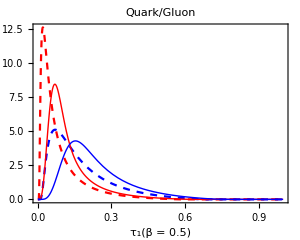
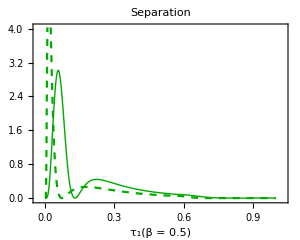

```mathematica
β test = 1.0001;
{QGClassifierSeparation["parton", "baseline", R baseline,Q baseline,β test],QGClassifierSeparation["hadron", "baseline",R baseline,Q baseline, β test]}
{
Plot[{AngularitiesDifferentialInterpolation["parton", "baseline","quark",R baseline,Q baseline,β test][τ1],
AngularitiesDifferentialInterpolation["parton", "baseline","gluon",R baseline,Q baseline,β test][τ1],
AngularitiesDifferentialInterpolation["hadron", "baseline","quark",R baseline,Q baseline,β test][τ1],
AngularitiesDifferentialInterpolation["hadron", "baseline","gluon",R baseline,Q baseline,β test][τ1]
},{τ1,τ1diff/2.0,τ1max-τ1diff/2.0},PlotLabel-> "Quark/Gluon",
PlotRange->All,PlotStyle->{Directive[Dashed, Red],Directive[Dashed, Blue],Directive[Thick, Red],Directive[Thick, Blue]}, Frame-> True, FrameStyle -> Thickness[Medium], FrameLabel->{"τ_1(β = 0.5)", ""}, ImageSize -> 300, PlotTheme->{ "Scientific","Frame"}, AspectRatio-> 0.8]
,
Plot[{(AngularitiesDifferentialInterpolation["parton", "baseline","quark",R baseline,Q baseline,β test][τ1] - AngularitiesDifferentialInterpolation["parton", "baseline","gluon",R baseline,Q baseline,β test][τ1])^2/(2(AngularitiesDifferentialInterpolation["parton", "baseline","quark",R baseline,Q baseline,β test][τ1] + AngularitiesDifferentialInterpolation["parton", "baseline","gluon",R baseline,Q baseline,β test][τ1] + 0.000000000001)),
(AngularitiesDifferentialInterpolation["hadron", "baseline","quark",R baseline,Q baseline,β test][τ1] - AngularitiesDifferentialInterpolation["hadron", "baseline","gluon",R baseline,Q baseline,β test][τ1])^2/(2(AngularitiesDifferentialInterpolation["hadron", "baseline","quark",R baseline,Q baseline,β test][τ1] + AngularitiesDifferentialInterpolation["hadron", "baseline","gluon",R baseline,Q baseline,β test][τ1] + 0.000000000001))},{τ1,τ1diff/2.0,τ1max-τ1diff/2.0},PlotLabel-> "Separation",
PlotStyle->{Directive[Dashed,Darker[Green]],Directive[Thick,Darker[Green]]}, Frame-> True, FrameStyle -> Thickness[Medium], FrameLabel->{"τ_1(β = 0.5)", ""}, ImageSize -> 300, PlotTheme->{ "Scientific","Frame"}, AspectRatio-> 0.8, PlotRange-> {{-0.03,1.03}, {-0.03,4.03}}]
}
```

{QGClassifierSeparation[parton,baseline,0.6,200.,0.5],QGClassifierSeparation[hadron,baseline,0.6,200.,0.5]}

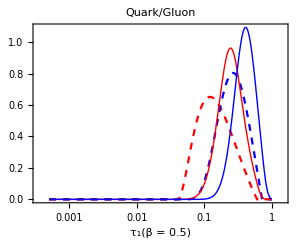

```mathematica
{QGClassifierSeparation["parton", "baseline",R baseline,Q baseline, β baseline],QGClassifierSeparation["hadron", "baseline",R baseline,Q baseline, β baseline]}

LogLinearPlot[{AngularitiesDifferentialInterpolation["parton", "baseline","quark",R baseline,Q baseline,β baseline][τ1]*τ1,
AngularitiesDifferentialInterpolation["parton", "baseline","gluon",R baseline,Q baseline,β baseline][τ1]*τ1,
AngularitiesDifferentialInterpolation["hadron", "baseline","quark",R baseline,Q baseline,β baseline][τ1]*τ1,
AngularitiesDifferentialInterpolation["hadron", "baseline","gluon",R baseline,Q baseline,β baseline][τ1]*τ1
},{τ1,τ1diff/2.0,τ1max-τ1diff/2.0},PlotLabel-> "Quark/Gluon",
PlotRange->All,PlotStyle->{Directive[Dashed, Red],Directive[Dashed, Blue],Directive[Thick, Red],Directive[Thick, Blue]}, Frame-> True, FrameStyle -> Thickness[Medium], FrameLabel->{"τ_1(β = 0.5)", ""}, ImageSize -> 300, PlotTheme->{ "Scientific","Frame"}, AspectRatio-> 0.8]
```

```mathematica
{QGClassifierSeparation["hadron", "baseline",R baseline,Q baseline, 0.5],QGClassifierSeparation["hadron", "baseline",R baseline,Q baseline, βone],QGClassifierSeparation["hadron", "baseline",R baseline,Q baseline, 2.0]}
{QGClassifierSeparation["hadron", "nogqq", R baseline,Q baseline,0.5],QGClassifierSeparation["hadron", "nogqq",R baseline,Q baseline, βone],QGClassifierSeparation["hadron", "nogqq", R baseline,Q baseline,2.0]}
{QGClassifierSeparation["hadron", "no2loop",R baseline,Q baseline, 0.5],QGClassifierSeparation["hadron", "no2loop",R baseline,Q baseline, βone],QGClassifierSeparation["hadron", "no2loop",R baseline,Q baseline, 2.0]}
```

{QGClassifierSeparation[hadron,baseline,0.6,200.,0.5],QGClassifierSeparation[hadron,baseline,0.6,200.,1.0001],QGClassifierSeparation[hadron,baseline,0.6,200.,2.]}

{QGClassifierSeparation[hadron,nogqq,0.6,200.,0.5],QGClassifierSeparation[hadron,nogqq,0.6,200.,1.0001],QGClassifierSeparation[hadron,nogqq,0.6,200.,2.]}

{QGClassifierSeparation[hadron,no2loop,0.6,200.,0.5],QGClassifierSeparation[hadron,no2loop,0.6,200.,1.0001],QGClassifierSeparation[hadron,no2loop,0.6,200.,2.]}

```mathematica
(* Q sweep *)
QGClassifierSeparation["hadron", "baseline",R baseline,#, β baseline]&/@ Q values

(* R sweep *)
QGClassifierSeparation["hadron", "baseline",#,Q baseline, β baseline]&/@ R values
(* αs sweep *)
{QGClassifierSeparation["hadron", "alphasx08", R baseline,Q baseline, β baseline],
QGClassifierSeparation["hadron", "alphasx09",R baseline,Q baseline, β baseline],
QGClassifierSeparation["hadron", "alphasx10",R baseline,Q baseline, β baseline],
QGClassifierSeparation["hadron", "alphasx11",R baseline,Q baseline, β baseline],
QGClassifierSeparation["hadron", "alphasx12",R baseline,Q baseline, β baseline]}
```

{QGClassifierSeparation[hadron,baseline,0.6,50,0.5],QGClassifierSeparation[hadron,baseline,0.6,100,0.5],QGClassifierSeparation[hadron,baseline,0.6,200,0.5],QGClassifierSeparation[hadron,baseline,0.6,400,0.5],QGClassifierSeparation[hadron,baseline,0.6,800,0.5]}

{QGClassifierSeparation[hadron,baseline,0.2,200.,0.5],QGClassifierSeparation[hadron,baseline,0.4,200.,0.5],QGClassifierSeparation[hadron,baseline,0.6,200.,0.5],QGClassifierSeparation[hadron,baseline,0.8,200.,0.5],QGClassifierSeparation[hadron,baseline,1.,200.,0.5]}

{QGClassifierSeparation[hadron,alphasx08,0.6,200.,0.5],QGClassifierSeparation[hadron,alphasx09,0.6,200.,0.5],QGClassifierSeparation[hadron,alphasx10,0.6,200.,0.5],QGClassifierSeparation[hadron,alphasx11,0.6,200.,0.5],QGClassifierSeparation[hadron,alphasx12,0.6,200.,0.5]}

## Trying to get NP shift right

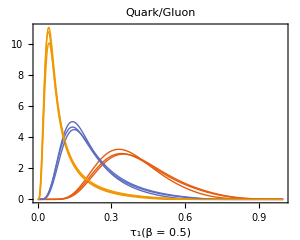

```mathematica
Plot[{
AngularitiesDifferentialInterpolation["hadron", "baseline","gluon",R baseline, 200,0.5][τ1],
AngularitiesDifferentialInterpolation["hadron", "baseline","gluon",R baseline, 200,βone][τ1],
AngularitiesDifferentialInterpolation["hadron", "baseline","gluon",R baseline, 200,2.0][τ1]
},{τ1,τ1diff/2.0,τ1max-τ1diff/2.0},PlotLabel-> "Quark/Gluon",
PlotRange->All,PlotStyle->Thick, Frame-> True, FrameStyle -> Thickness[Medium], FrameLabel->{"τ_1(β = 0.5)", ""}, ImageSize -> 300, PlotTheme->{ "Scientific","Frame"}, AspectRatio-> 0.8];
Plot[{
AngularitiesDifferentialInterpolation["hadron", "no2loop","gluon",R baseline, 200,0.5][τ1],
AngularitiesDifferentialInterpolation["hadron", "no2loop","gluon",R baseline, 200,βone][τ1],
AngularitiesDifferentialInterpolation["hadron", "no2loop","gluon",R baseline, 200,2.0][τ1]
},{τ1,τ1diff/2.0,τ1max-τ1diff/2.0},PlotLabel-> "Quark/Gluon",
PlotRange->All,PlotStyle->Thick, Frame-> True, FrameStyle -> Thickness[Medium], FrameLabel->{"τ_1(β = 0.5)", ""}, ImageSize -> 300, PlotTheme->{ "Scientific","Frame"}, AspectRatio-> 0.8];
Plot[{
AngularitiesDifferentialInterpolation["hadron", "nogqq","gluon",R baseline, 200,0.5][τ1],
AngularitiesDifferentialInterpolation["hadron", "nogqq","gluon",R baseline, 200,βone][τ1],
AngularitiesDifferentialInterpolation["hadron", "nogqq","gluon",R baseline, 200,2.0][τ1]
},{τ1,τ1diff/2.0,τ1max-τ1diff/2.0},PlotLabel-> "Quark/Gluon",
PlotRange->All,PlotStyle->Thick, Frame-> True, FrameStyle -> Thickness[Medium], FrameLabel->{"τ_1(β = 0.5)", ""}, ImageSize -> 300, PlotTheme->{ "Scientific","Frame"}, AspectRatio-> 0.8];

Show[%,%%,%%%]


(*Plot[{
AngularitiesDifferentialInterpolation["hadron", "nogqq","gluon",R baseline, 50,0.5][τ1],
AngularitiesDifferentialInterpolation["hadron", "nogqq","gluon",R baseline, 50,βone][τ1],
AngularitiesDifferentialInterpolation["hadron", "nogqq","gluon",R baseline, 50,2.0][τ1]
},{τ1,τ1diff/2.0,τ1max-τ1diff/2.0},PlotLabel-> "Quark/Gluon",
PlotRange->All,PlotStyle->Thick, Frame-> True, FrameStyle -> Thickness[Medium], FrameLabel->{"τ_1(β = 0.5)", ""}, ImageSize -> 300, PlotTheme->{ "Scientific","Frame"}, AspectRatio-> 0.8]*)
```

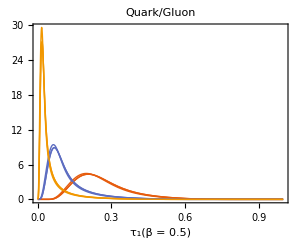

```mathematica
Plot[{
AngularitiesDifferentialInterpolation["hadron", "baseline","quark",R baseline, 200,0.5][τ1],
AngularitiesDifferentialInterpolation["hadron", "baseline","quark",R baseline, 200,βone][τ1],
AngularitiesDifferentialInterpolation["hadron", "baseline","quark",R baseline, 200,2.0][τ1]
},{τ1,τ1diff/2.0,τ1max-τ1diff/2.0},PlotLabel-> "Quark/Gluon",
PlotRange->All,PlotStyle->Thick, Frame-> True, FrameStyle -> Thickness[Medium], FrameLabel->{"τ_1(β = 0.5)", ""}, ImageSize -> 300, PlotTheme->{ "Scientific","Frame"}, AspectRatio-> 0.8];
Plot[{
AngularitiesDifferentialInterpolation["hadron", "no2loop","quark",R baseline, 200,0.5][τ1],
AngularitiesDifferentialInterpolation["hadron", "no2loop","quark",R baseline, 200,βone][τ1],
AngularitiesDifferentialInterpolation["hadron", "no2loop","quark",R baseline, 200,2.0][τ1]
},{τ1,τ1diff/2.0,τ1max-τ1diff/2.0},PlotLabel-> "Quark/Gluon",
PlotRange->All,PlotStyle->Thick, Frame-> True, FrameStyle -> Thickness[Medium], FrameLabel->{"τ_1(β = 0.5)", ""}, ImageSize -> 300, PlotTheme->{ "Scientific","Frame"}, AspectRatio-> 0.8];
Plot[{
AngularitiesDifferentialInterpolation["hadron", "nogqq","quark",R baseline, 200,0.5][τ1],
AngularitiesDifferentialInterpolation["hadron", "nogqq","quark",R baseline, 200,βone][τ1],
AngularitiesDifferentialInterpolation["hadron", "nogqq","quark",R baseline, 200,2.0][τ1]
},{τ1,τ1diff/2.0,τ1max-τ1diff/2.0},PlotLabel-> "Quark/Gluon",
PlotRange->All,PlotStyle->Thick, Frame-> True, FrameStyle -> Thickness[Medium], FrameLabel->{"τ_1(β = 0.5)", ""}, ImageSize -> 300, PlotTheme->{ "Scientific","Frame"}, AspectRatio-> 0.8];

Show[%,%%,%%%]
```